Polinomio de Lagrange

### Autores : Helver Jussef López Abril Michael Velasquez Rico

Este programa calcula el polinomio de interpolación de Lagrange para cuatro puntos y muestra su grafica :

```mathematica
f[x_]=ⅇ^x;
```

```mathematica
Subscript[L, 0][x_]:=((x-Subscript[x, 1])*(x-Subscript[x, 2])*(x-Subscript[x, 3]))/((Subscript[x, 0]-Subscript[x, 1])*(Subscript[x, 0]-Subscript[x, 2])*(Subscript[x, 0]-Subscript[x, 3])); 
Subscript[L, 1][x_]:=((x-Subscript[x, 0])*(x-Subscript[x, 2])*(x-Subscript[x, 3]))/((Subscript[x, 1]-Subscript[x, 0])*(Subscript[x, 1]-Subscript[x, 2])*(Subscript[x, 1]-Subscript[x, 3]));
```

```mathematica
Subscript[L, 2][x_]:=((x-Subscript[x, 1])*(x-Subscript[x, 2])*(x-Subscript[x, 3]))/((Subscript[x, 2]-Subscript[x, 0])*(Subscript[x, 2]-Subscript[x, 1])*(Subscript[x, 2]-Subscript[x, 3]));
```

```mathematica
Subscript[L, 3][x_]:=((x-Subscript[x, 0])*(x-Subscript[x, 1])*(x-Subscript[x, 2]))/((Subscript[x, 3]-Subscript[x, 0])*(Subscript[x, 3]-Subscript[x, 1])*(Subscript[x, 3]-Subscript[x, 2]));
```

```mathematica
Subscript[x, 0]=1; 
Subscript[x, 1]=2;
Subscript[x, 2]=3;
Subscript[x, 3]=4;
```

```mathematica
Subscript[L, 0][x]
```

-1/6 (-4+x) (-3+x) (-2+x)

```mathematica
Subscript[L, 1][x]
```

1/2 (-4+x) (-3+x) (-1+x)

```mathematica
Subscript[L, 2][x]
```

-1/2 (-4+x) (-3+x) (-2+x)

```mathematica
Subscript[L, 3][x]
```

1/6 (-3+x) (-2+x) (-1+x)

```mathematica
f[1]
```

ⅇ

```mathematica
f[2]
```

ⅇ^2

```mathematica
f[3]
```

ⅇ^3

```mathematica
f[4]
```

ⅇ^4

```mathematica
Subscript[P, 4][x]= f[Subscript[x, 0]]*Subscript[L, 0][x]+f[Subscript[x, 1]]Subscript[L, 1][x]+f[Subscript[x, 2]]Subscript[L, 2][x]+f[Subscript[x, 3]]Subscript[L, 3][x]
```

-1/6 ⅇ (-4+x) (-3+x) (-2+x)-1/2 ⅇ^3 (-4+x) (-3+x) (-2+x)+1/2 ⅇ^2 (-4+x) (-3+x) (-1+x)+1/6 ⅇ^4 (-3+x) (-2+x) (-1+x)

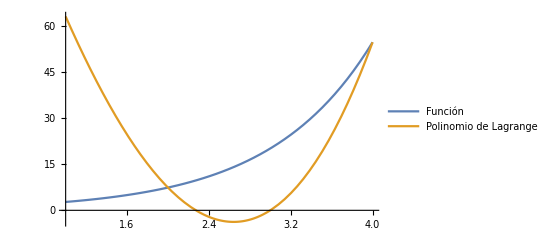

```mathematica
Plot[{f[x],-1/6 ⅇ (-4+x) (-3+x) (-2+x)-1/2 ⅇ^3 (-4+x) (-3+x) (-2+x)+1/2 ⅇ^2 (-4+x) (-3+x) (-1+x)+1/6 ⅇ^4 (-3+x) (-2+x) (-1+x)},{x,1,4},PlotLegends->LineLegend[{"Función","Polinomio de Lagrange"},LegendFunction->Frame]]
```